# Exploring Neural Networks in the Wolfram Language

# Start: 3pm (CDT)

```mathematica
NormalDistribution[0,1]
```

NormalDistribution[0,1]

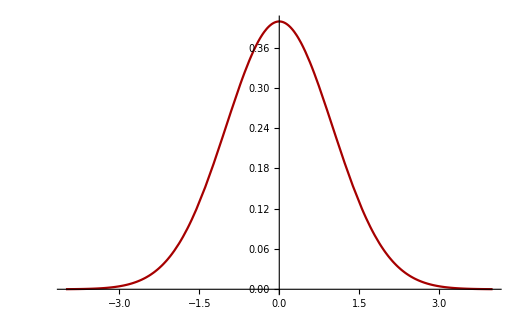

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

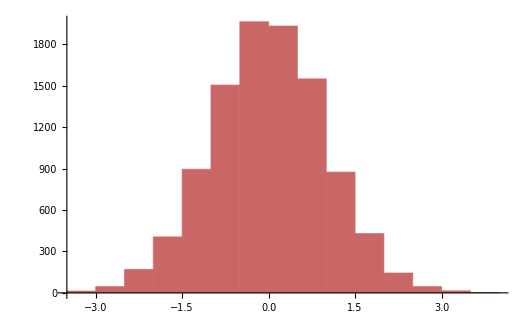

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],10000]]
```

```mathematica
sample[center_,num_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],num];
```

```mathematica
sample[{0,0},10]
```

{{0.0834816,0.71781},{-1.13905,0.846658},{-0.348369,-1.16366},{-1.53333,-1.00682},{0.670374,0.698389},{-0.0534056,-0.0329694},{-0.0994104,-1.80077},{-0.283355,0.629171},{1.18469,-1.41661},{2.06469,2.19507}}

```mathematica
clusters={sample[{-1,-1},10000],sample[{1,1},10000]};
```

```mathematica
MapThread[f,{{1,2,3},{a,b,c}}]
```

{f[1,a],f[2,b],f[3,c]}

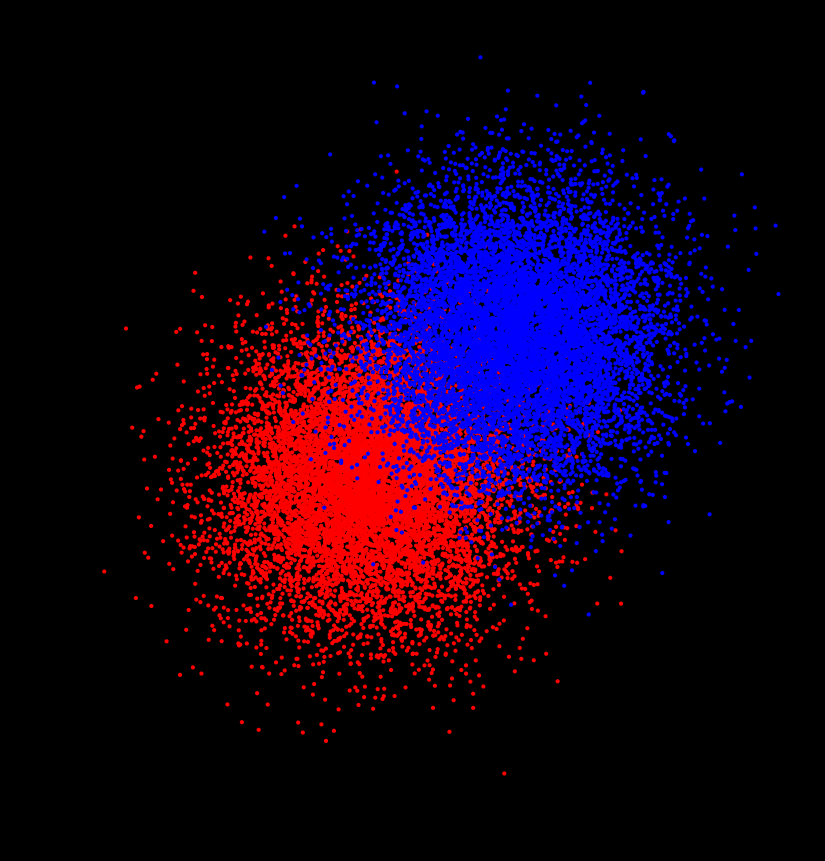

```mathematica
Graphics[MapThread[{#1,Point[#2]}&,{{Red,Blue},clusters}],Axes->True,PlotRange->10,Background->Black]
```

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{Red,Blue}}]
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
net[{-1,-1}]
```

RGBColor[0, 0, 1]

```mathematica
{{x1,y1}->Red,{x2,y2}->Blue,...}
```

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,Blue}}
]];
```

```mathematica
data[[;;10]]
```

{{-0.456847,1.89191}→RGBColor[0, 0, 1],{1.54609,4.03157}→RGBColor[0, 0, 1],{-1.65431,-0.750348}→RGBColor[1, 0, 0],{1.15422,1.1536}→RGBColor[0, 0, 1],{1.10749,3.77804}→RGBColor[0, 0, 1],{0.959273,3.21067}→RGBColor[0, 0, 1],{-2.44591,0.0274889}→RGBColor[1, 0, 0],{-1.45608,-1.61841}→RGBColor[1, 0, 0],{0.486221,2.86318}→RGBColor[0, 0, 1],{0.496548,0.41299}→RGBColor[0, 0, 1]}

```mathematica
training=data[[1;;18000]];
validation=data[[18000;;20000]];
```

```mathematica
result=NetTrain[net,training,ValidationSet->validation]
```

NetChain[]

```mathematica
result[{-.1,-.1},"Probabilities"]
```

<|RGBColor[1, 0, 0]→0.579611,RGBColor[0, 0, 1]→0.420388|>

```mathematica
result[{-.1,-.1}]
```

RGBColor[1, 0, 0]

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.921539

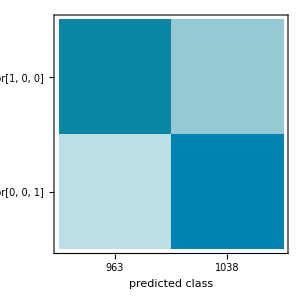

```mathematica
cm["ConfusionMatrixPlot"]
```